NonlinearModelFit::precw: The precision of the data and model function (MachinePrecision) is less than the specified WorkingPrecision (40).

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (40).

--- Riesz-Weyl Reconstruction (N=8000) ---

Koeffizient | Rekonstruiert | Target | Fehler %

A0 (Vol)    | 0.058207701 | 0.058259681 | 0.08922

A1 (Area)   | -0.28322171 | -0.28846833 | -1.819

A2 (Curv)   | 0.21154101 | 0.031830989 | 564.6

FittedModel::precw: The precision of the argument function (MachinePrecision) is less than WorkingPrecision (40).

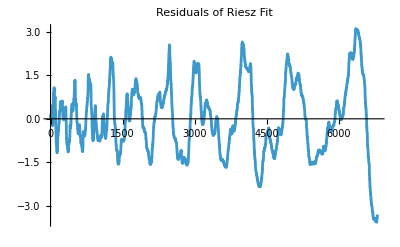

```mathematica
Clear["Global`*"];

(*1. Daten laden*)
path="C:\\Users\\sulta\\git\\cone-operator-lab\\data\\eigenvalues\\box_eigs_exact_8000.txt";
eigs=Sort@Flatten@Import[path,"Table"];
ks=Sqrt[eigs];
ns=Range[Length[ks]];

(*2. Riesz-Mittelung (2. Ordnung)*)
(*Das Integral der Zählfunktion glättet die Spektralstufen perfekt*)
(*Theoretisch:R(k)=Integrate[N(v),{v,0,k}]*)
rieszK=Accumulate[ns*Differences[Prepend[ks,0.0]]];

(*3. Das Modell für das Integral der Weyl-Reihe*)
(*N(k)=a0*k^3+a1*k^2+a2*k+a3*)
(* ->R(k)=(a0/4)*k^4+(a1/3)*k^3+(a2/2)*k^2+a3*k+a4*)
model=(a0/4)*k^4+(a1/3)*k^3+(a2/2)*k^2+a3*k+a4;

(*4. Fit im stabilen Fenster*)
(*Wir ignorieren die ersten 200 (Einschwingen) und letzten 1000 (Cut-off)*)
fitRange=200;;7000;
fitData=Transpose[{ks[[fitRange]],rieszK[[fitRange]]}];

fit=NonlinearModelFit[fitData,model,{a0,a1,a2,a3,a4},k,WorkingPrecision->40];

{recA0,recA1,recA2}={a0,a1,a2}/. fit["BestFitParameters"];

(*5. Vergleich mit den Quader-Targets*)
{a,b,c}={1.0,1.5,2.3};
tA0=(a*b*c)/(6*Pi^2);
tA1=-(2*(a*b+a*c+b*c))/(16*Pi);
tA2=((Pi/4)*(a+b+c))/(12*Pi^2);

Print["--- Riesz-Weyl Reconstruction (N=8000) ---"];
Print["Koeffizient | Rekonstruiert | Target | Fehler %"];
Print["A0 (Vol)    | ",NumberForm[recA0,8]," | ",NumberForm[tA0,8]," | ",NumberForm[Abs[recA0-tA0]/tA0*100,4]];
Print["A1 (Area)   | ",NumberForm[recA1,8]," | ",NumberForm[tA1,8]," | ",NumberForm[Abs[recA1-tA1]/tA1*100,4]];
Print["A2 (Curv)   | ",NumberForm[recA2,8]," | ",NumberForm[tA2,8]," | ",NumberForm[Abs[recA2-tA2]/tA2*100,4]];

(*6. Visuelle Kontrolle des Residuums*)
ListLinePlot[fit["FitResiduals"],PlotLabel->"Residuals of Riesz Fit",PlotRange->All]
```